```mathematica
(*Пункт 6*)
Clear["Global`*"]
```

```mathematica
nMat=1.444;
k0=2Pi/1.55;
l=0;
rMax=25;
rCore=8.2/2;
percn=0.0036;
c=3*10^8/1000/10^12;
```

```mathematica
V=((2*π*rCore/1.55)^2*2*nMat*percn*nMat)^0.5;
```

```mathematica
n[r_]=(percn*HeavisideTheta[rCore-r]+1)*nMat;
```

```mathematica
op=(R''[r]+(1/r)*R'[r]+k0^2*(n[r])^2*R[r]);
```

```mathematica
{values,vectors}=NDEigensystem[R''[r]+(1/r)*R'[r]+k0^2*(n[r])^2*R[r],R[r],{r,0,rMax},100]
```

NDEigensystem::maxeigen: A maximum number of 41 eigenvalues and functions can be computed for this discretized system.

{{-0.270102,1.82809,-2.04359,-3.34263,-4.03649,4.10974,6.45804,8.78621,11.0351,13.1669,-13.7614,15.1587,16.9987,18.684,20.2195,21.6156,22.884,24.0326,25.0593,25.9335,26.5086,28.1862,28.778,29.3903,29.9743,30.5185,31.0197,31.4783,31.8976,32.2817,32.6325,32.9493,33.2301,33.4738,33.6824,33.8599,34.0094,34.129,34.2147,34.2603,34.3694},{InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r],InterpolatingFunction[{{0., 25.}}, <>][r]}}

```mathematica
Sqrt[values[[41]]]/k0
```

1.44623

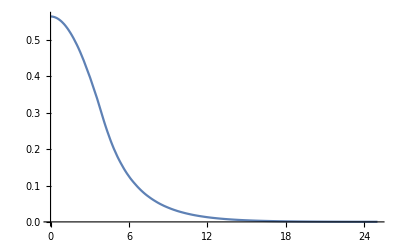

```mathematica
Plot[vectors[[41]],{r,0,rMax}]
```